# Gráficas agujeros negros de tercer orden en la curvatura

### Solución reescalada

```mathematica
f3rees1[r2_,μ_,α_,b_]:=1+r2^2+(36 (7-108 b) b r2^4 α^2)/(7 (-46656/7 b^3 (-7+162 b) r2^6 α^6+(629856 b^3 √(-7+144 b) (49+54 b (-21+√21 √(-7+144 b)))^(4/3) r2^2 α^5 μ)/(7^(1/3) (-7 √21+162 b (√21-√(-7+144 b))) (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3)))+69984/7 b^3 r2^2 α^(9/2) √(3888/7 b^2 (-7+144 b) r2^8 α^3+(12 7^(2/3) √(-7+144 b) (-7+162 b) (49+54 b (-21+√21 √(-7+144 b)))^(4/3) r2^4 α^2 μ)/((7 √21-162 b (√21-√(-7+144 b))) (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3)))+(567 7^(1/3) (-7+144 b) (49+54 b (-21+√21 √(-7+144 b)))^(8/3) α μ^2)/((7 √21-162 b (√21-√(-7+144 b)))^2 (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3))^2)))^(1/3))+1/(36 b α^2)(-46656/7 b^3 (-7+162 b) r2^6 α^6+(629856 b^3 √(-7+144 b) (49+54 b (-21+√21 √(-7+144 b)))^(4/3) r2^2 α^5 μ)/(7^(1/3) (-7 √21+162 b (√21-√(-7+144 b))) (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3)))+69984/7 b^3 r2^2 α^(9/2) √(3888/7 b^2 (-7+144 b) r2^8 α^3+(12 7^(2/3) √(-7+144 b) (-7+162 b) (49+54 b (-21+√21 √(-7+144 b)))^(4/3) r2^4 α^2 μ)/((7 √21-162 b (√21-√(-7+144 b))) (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3)))+(567 7^(1/3) (-7+144 b) (49+54 b (-21+√21 √(-7+144 b)))^(8/3) α μ^2)/((7 √21-162 b (√21-√(-7+144 b)))^2 (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3))^2)))^(1/3)
df3rees[r2_,μ_,α_,b_]:=Simplify[D[f3rees1[r2,μ,α,b],r2]]
```

### Iteración

```mathematica
alphaVals={0.03,0.1,0.5};
bVals={0.07,0.1,0.5};
sistema[r2_,μ_,α_,b_]:={f3rees1[r2,μ,α,b]==0,df3rees[r2,μ,α,b]==0};
```

```mathematica
For[i=1,i<=Length[alphaVals],i++,
For[j=1,j<=Length[bVals],j++,
f=f3rees1[r2,μ,alphaVals[[i]],bVals[[j]]];
df=df3rees[r2,μ,alphaVals[[i]],bVals[[j]]];
sol=NSolve[{f==0,df==0,r2>0,μ>0},{r2,μ},Reals];
resultados[i,j]=sol[[1]]
]
]
```

```mathematica
N[resultados[3,3][[1]]]
```

μ→0.701189

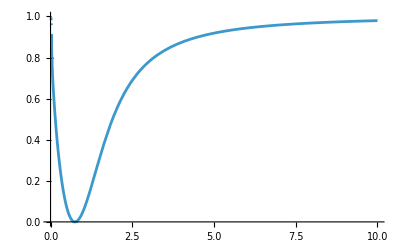

```mathematica
Plot[f3rees1[r2,0.02199999999997881,alphaVals[[1]],bVals[[1]]],{r2,0,10}]
```